```mathematica
f[x_]:=Exp[x] /x+ 2x^2 Sin[x];
```

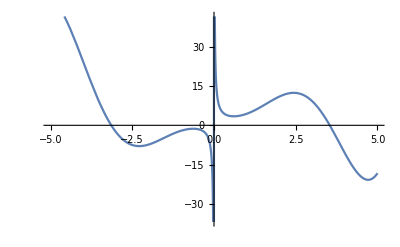

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
Table[N[D[f[x],{x,k}]/.x->1,17],{k, 0, 14}]
```

{4.4012237980748382,4.4464885509678655,8.723642245019956,-10.131192415931451,-2.6926621035325515,-123.30646837902937,782.11725700134034,-5018.9509084565035,40210.422879416369,-362926.18094394889,3.628971621929046×10^6,-3.9916719028555494×10^7,4.7900135379519123×10^8,-6.2270209235552409×10^9,8.7178291535039949×10^10}

```mathematica
(*
Haskell: 
f (idD 1);
4.401223798074838,4.4464885509678655,8.723642245019956,-10.131192415931453,-2.692662103532559,-123.30646837902931,782.1172570013406,-5018.950908456501,40210.42287941638,-362926.1809439487,3628971.6219290467,-3.991671902855549e7,4.7900135379519105e8,-6.227020923555244e9,8.71782915350399e10, ...
*)
```

```mathematica
(*
Kjer ni odvedljiva lahko dobimo čudne stvari:
Infinity,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN
*)
```

```mathematica
f[x_]:=Exp[x] /x+ 2x^2 Sin[x];
```

```mathematica
Plot[f[x],{x,-5,5}]
```

-Graphics-

```mathematica
Table[N[D[f[x],{x,k}]/.x->0.01,17],{k, 0, 14}]
```

{101.005,-9999.5,2.×10^6,-6.×10^8,2.4×10^11,-1.2×10^14,7.2×10^16,-5.04×10^19,4.032×10^22,-3.6288×10^25,3.6288×10^28,-3.99168×10^31,4.79002×10^34,-6.22702×10^37,8.71783×10^40}

```mathematica
(*
Haskell:
f (idD 0.01);
101.00501870838346,-9999.496054149928,2000000.4558366945,-5.999999877499917e8,2.399999999998017e11,-1.2000000000003981e14,7.2e16,-5.039999999999999e19,4.032000000000001e22,-3.6287999999999995e25,3.6288e28,-3.9916799999999992e31,4.790015999999998e34,-6.227020799999999e37,8.71782912e40, ...
*)
```

```mathematica
g[x_]:=Abs[x];
```

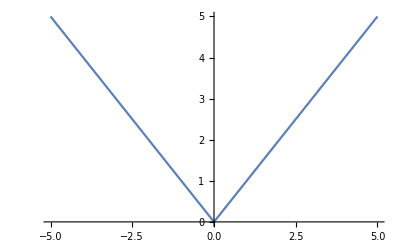

```mathematica
Plot[g[x],{x,-5,5}]
```

```mathematica
Table[N[D[g[x],{x,k}]/.x->0,17],{k, 0, 14}]
```

{0,Abs'[0],Abs''[0],Abs^(3)[0],Abs^(4)[0],Abs^(5)[0],Abs^(6)[0],Abs^(7)[0],Abs^(8)[0],Abs^(9)[0],Abs^(10)[0],Abs^(11)[0],Abs^(12)[0],Abs^(13)[0],Abs^(14)[0]}

```mathematica
(*
Kot vidimo, mathematica ne zna odvajati Abs. Limits pa lepo izračuna levi in desni odvod:
g (idD 0) = D  0.0 -1.0  1.0

*)

(*
Za generiranje neodvedljivih funkcij lahko uporabljamo tudi min/max. Kjer pa funkcija ni definirana (npr. v polu), pa odvodov ne znamo izračunati.
*)
```

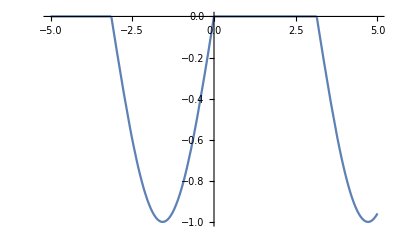

```mathematica
h[x_]:=Min[Sin[x],0];
Plot[h[x],{x,-5,5}]
```

```mathematica
D[h[x],x]
```

Piecewise[{{Cos[x], Sin[x]<0}, {0, True}}]

```mathematica
(*
Kot vidimo mathematica pravi, da je odvod v točki 0 enak 0, kar ni res (saj funkcija tam ni odvedljiva). Haskell pravi tole:
h (idD 0) = D 0.0 1.0 0.0
*)
```

```mathematica
(*
Nekatere funkcije znamo tudi integrirati (funkcijo lokalno omejimo z linearnimi funkcijami):
*)
```

```mathematica
ff[x_]:=Exp[x]*Sin[x];
```

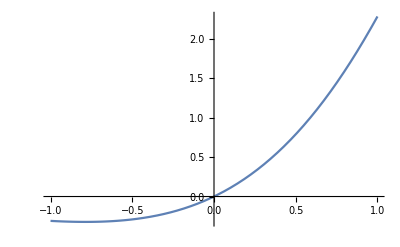

```mathematica
Plot[ff[x],{x,-1,1}]
```

```mathematica
N[Integrate[ff[x],{x,-1,1}],15]
```

0.663493666631241

```mathematica
(*
	h = 0.0001: 0.6634936650201322
h = 0.00001: 0.6634936666176671
*)
```

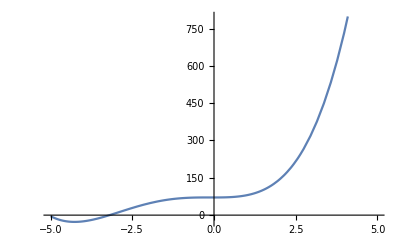

```mathematica
fg[x_]:= x^4+6x^3+2x^2 + 71;
Plot[fg[x],{x,-5,5}]
```

```mathematica
N[Integrate[fg[x],{x,-5,5}],15]
```

2126.66666666667

```mathematica
(*
	h = 0.0001: 2126.6666662342395
h = 0.00001: 2126.6666666970277
*)
```